RIGHT TRIANGLE

```mathematica
Module[{rPhase,rTie,rx1,rx2,ftie,interp,xPlait,rPlot},
rPhase:=Interpolation[Table[BezierFunction[{{0.1,0},{0.12,0.7},{0.37,0.46},{0.9,0}}][i],{i,0,1,0.025}]];

rTie[x_]:=0.017*n^2*x+0.0375*n;
rx1:=x/.FindRoot[rPhase[x]==rTie[x],{x,0.1}];
rx2:=x/.FindRoot[rPhase[x]==rTie[x],{x,0.9}];

ftie[x_]:=-(x-rx1)+rPhase[rx1];
interp:=Interpolation[Table[{rx2,ftie[rx2]},{n,1,6}]];
xPlait:=x/.Quiet@FindRoot[rPhase[x]==interp[x],{x,0.1}];

rPlot=Show[
Graphics[{
{GrayLevel[0.6],Table[{Line[{{0,i},{1-i,i}}],Line[{{i,0},{i,1-i}}],Line[{{0,i},{i,0}}]},{i,0,1,0.1}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,1},{0,0},{1,0}}]},
Table[{Text[Style[j,15],{j,-0.03}],Text[Style[j,15],{-0.035,j}]},{j,0.1,0.9,0.1}],

{PointSize[0.02],Table[Point[{rx2,ftie[rx2]}],{n,1,6}],Point[{xPlait,rPhase[xPlait]}]}

}],
Plot[rPhase[x],{x,0.1,0.9},PlotStyle->{Thick,Black}],
Table[Plot[rTie[x],{x,rx1,rx2},PlotStyle->{Thick,Black}],{n,1,6}],
AspectRatio->1,ImageSize->{470,450}];
{xPlait,rPhase[xPlait]}
]
```

{0.195596,0.410748}

EQUILATERAL TRIANGLE

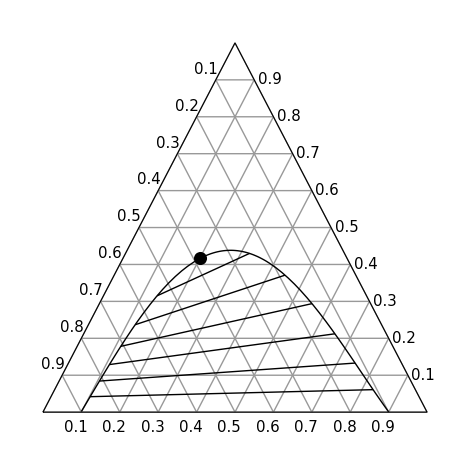

```mathematica
Module[{ePhase,eTie,ex1,ex2,ftie,interp,xPlait,equilateralPlot},
ePhase[x_]:=4.0108*x^4-7.5956*x^3+2.3721*x^2+1.2499*x-0.14;

eTie[x_]:=(0.0093*n^2+0.0131*n)*x+(-0.0017*n^2+0.0352*n);
ex1:=x/.FindRoot[ePhase[x]==eTie[x],{x,0.1}];
ex2:=x/.FindRoot[ePhase[x]==eTie[x],{x,0.9}];

ftie[x_]:=-(x-ex1)+ePhase[ex1];
interp:=Interpolation[Table[{ex2,ftie[ex2]},{n,1,6}]];
xPlait:=x/.Quiet@FindRoot[ePhase[x]==interp[x],{x,0.1}];

equilateralPlot=Show[
Graphics[{
{Thin,GrayLevel[0.6],Table[{Line[{{i/2,i*√3/2},{1-i/2,i*√3/2}}],Line[{{i,0},{i/2,i*√3/2}}],Line[{{1-i,0},{1-i/2,i*√3/2}}]},{i,0,1,0.1}]},
{EdgeForm[Thick],FaceForm[None],Polygon[{{0,0},{0.5,√3/2},{1,0}}]},
Table[{Text[Style[j,15],{1.04-j/2,j*√3/2}],Rotate[Text[Style[1-j,15],{j/2-0.025,j*√3/2+0.025}],-55 Degree],Rotate[Text[Style[j,15],{j-0.015,-0.035}],55 Degree]},{j,0.1,0.9,0.1}],
{PointSize[0.02],Point[{xPlait,ePhase[xPlait]}]}
}],
Plot[ePhase[x],{x,0.1,0.9},PlotStyle->{Thick,Black}],
Table[Plot[eTie[x],{x,ex1,ex2},PlotStyle->{Thick,Black}],{n,1,6}],
AspectRatio->1,ImageSize->{470,450}]
(*{xPlait,ePhase[xPlait]}*)
]
```